dg3[mhe4s,mhe4,mx2]/10^10=0.000382243

me3[mhe4s,mhe4,mx2]/10^10   =29.004

phs[mhe4s,mhe4,mx2]=0.000013179

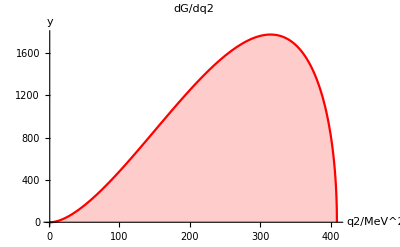

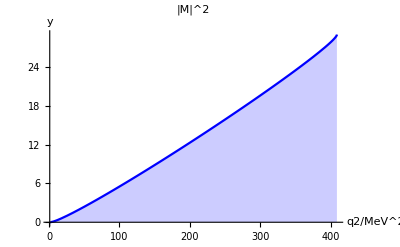

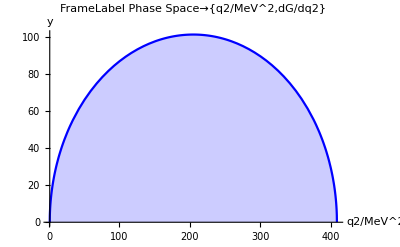

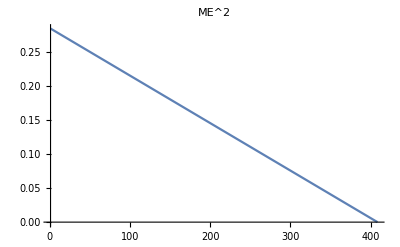

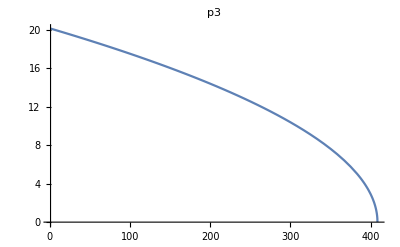

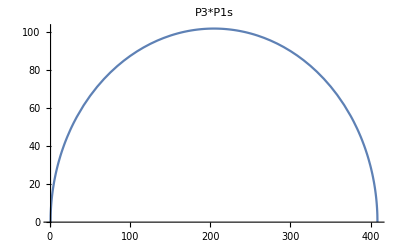

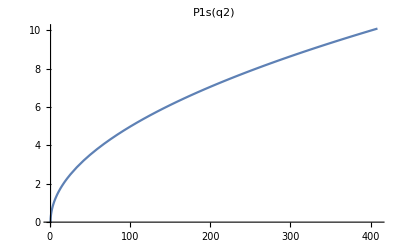

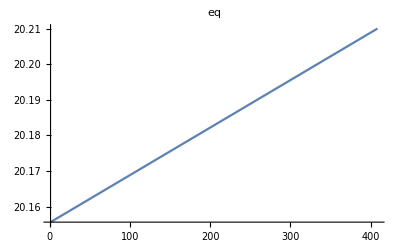

```mathematica
mbe8=8.005305*931.5;
mbe8s=mbe8+18.15;
mhe4=3727.409;
mhe4s=mhe4+20.21;
me= 0.00051099907*1000;

eq[m_,m3_,q2_]:=(m^2-m3^2+q2)/(2m);
pq[m_,m3_,q2_]:=Sqrt[eq[m,m3,q2]^2-q2];
p3[m_,m3_,q2_]:=pq[m,m3,q2];
e3[m_,m3_,q2_]:=Sqrt[p3[m,m3,q2]^2+m3^2];
p1s[q2_]:=Sqrt[q2/4-me^2];
e1s[q2_]:=Sqrt[q2]/2;
gamma[m_,m3_,q2_]:=eq[m,m3,q2]/Sqrt[q2];
vel[m_,m3_,q2_]:=Sqrt[eq[m,m3,q2]^2-q2]/eq[m,m3,q2];
p3q[m_,m3_,q2_]:=(m^2-m3^2-q2)/2.;
p1q[q2_]:=q2/2.;
p1p2[q2_]:=(q2-2me^2)/2.;
p3p1[m_,m3_,q2_]:=m*gamma[m,m3,q2]*Sqrt[q2]/2;
me2[m_,m3_,q2_]:=2*p3p1[m,m3,q2]*(p3q[m,m3,q2]-p3p1[m,m3,q2])-m3^2*(q2-2me^2)/2-me^2*m3^2;
me22[m_,m3_,q2_]:=2*(m*eq[m,m3,q2]/2)^2-m3^2*(q2-2me^2)/2-me^2*m3^2;
me3[m_,m3_,q2_]:=2*( (m*gamma[m,m3,q2])^2 *(e1s[q2]^2-(vel[m,m3,q2]*p1s[q2]*2/3))^2)-m3^2*(q2-2me^2)/2-me^2*m3^2;
q2min=(2me)^2;
q2max=(mhe4s-mhe4)^2;


dg[m_,m3_,q2_]:=me2[m,m3,q2]*p3[m,m3,q2]*p1s[q2];
dg3[m_,m3_,q2_]:=me3[m,m3,q2]*p3[m,m3,q2]*p1s[q2];
(*Plot[dg[mhe4s,mhe4,q2]/10^10,                     {q2,q2min,q2max},PlotLabel->"dG/dq2",FrameLabel->{"q2/MeV^2","dG/dq2"}]*)

mx2=q2max;
Print["dg3[mhe4s,mhe4,mx2]/10^10=",dg3[mhe4s,mhe4,mx2]/10^10]
Print["me3[mhe4s,mhe4,mx2]/10^10   =",  me3[mhe4s,mhe4,mx2]/10^10 ]
Print["phs[mhe4s,mhe4,mx2]=",phs[mhe4s,mhe4,mx2]]

Plot[dg3[mhe4s,mhe4,q2]/10^10,                     {q2,q2min,q2max},
PlotLabel->"dG/dq2",
FrameLabel->{"q2/MeV^2","dG/dq2"},
PlotRange->{{q2min,q2max},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"q2/MeV^2",y},
PlotStyle->{Blue,Red}
]

Plot[me3[mhe4s,mhe4,q2]/10^10,                   {q2,q2min,q2max},
PlotLabel->"|M|^2",
FrameLabel->{"q2/MeV^2","dG/dq2"},
PlotRange->{{q2min,q2max},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"q2/MeV^2",y},
PlotStyle->{Blue}
]
Plot[phs[mhe4s,mhe4,q2],                   {q2,q2min,q2max},
PlotLabel->"Phase Space"
FrameLabel->{"q2/MeV^2","dG/dq2"},
PlotRange->{{q2min,q2max},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"q2/MeV^2",y},
PlotStyle->{Blue}
]




Plot[me2[mhe4s,mhe4,q2]/10^10,                   {q2,q2min,q2max},PlotLabel->"ME^2"]




Plot[p3[mhe4s,mhe4,q2],                   {q2,q2min,q2max},PlotLabel->"p3"]
Plot[p3[mhe4s,mhe4,q2]*p1s[q2], {q2,q2min,q2max},PlotLabel->"P3*P1s"]
Plot[p1s[q2],                                              {q2,q2min,q2max},PlotLabel->"P1s(q2)"]

Plot[eq[mhe4s,mhe4,q2],                 {q2,q2min,q2max},PlotLabel->"eq"]
Plot[pq[mhe4s,mhe4,q2],                  {q2,q2min,q2max},PlotLabel->"pq"]

Plot[e3[mhe4s,mhe4,q2],                   {q2,q2min,q2max},PlotLabel->"e3"]

Plot[gamma[mhe4s,mhe4,q2],             {q2,q2min,q2max},PlotLabel->"gamma"]
Plot[vel[mhe4s,mhe4,q2],                  {q2,q2min,q2max},PlotLabel->"velocity"]
Plot[p3q[mhe4s,mhe4,q2],                  {q2,q2min,q2max},PlotLabel->"p3q"]
Plot[p3p1[mhe4s,mhe4,q2],                  {q2,q2min,q2max},PlotLabel->"p3p1"]
Plot[p1q[q2],                                             {q2,q2min,q2max},PlotLabel->"p1q"]
```

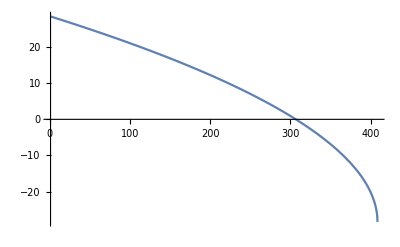

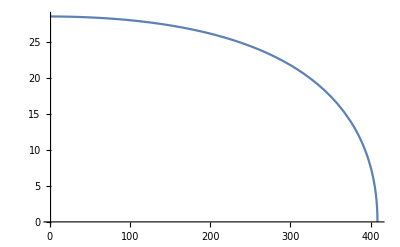

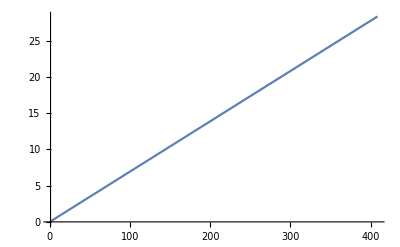

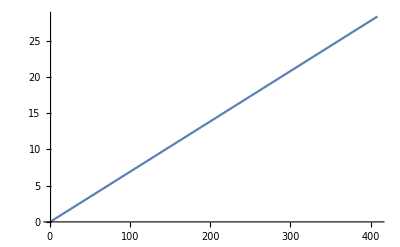

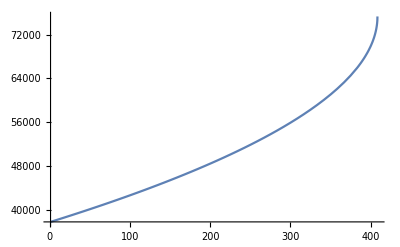

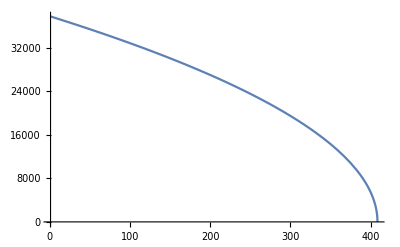

```mathematica
Plot[(2*p3p1[mhe4s,mhe4,q2]*(p3q[mhe4s,mhe4,q2]-p3p1[mhe4s,mhe4,q2])-mhe4^2*(q2-2me^2)/2-me^2*mhe4^2)/10^8,{q2,q2min,q2max}]
Plot[(2*p3p1[mhe4s,mhe4,q2]*(p3q[mhe4s,mhe4,q2]-p3p1[mhe4s,mhe4,q2]))/10^8,{q2,q2min,q2max}]
Plot[(mhe4^2*(q2-2me^2)/2+me^2*mhe4^2)/10^8,{q2,q2min,q2max}]
Plot[mhe4^2*(q2-2me^2)/2/10^8,{q2,q2min,q2max}]
Plot[(p3q[mhe4s,mhe4,q2]-p3p1[mhe4s,mhe4,q2]),{q2,q2min,q2max}]
Plot[(p3p1[mhe4s,mhe4,q2]),{q2,q2min,q2max}]
```